# Data Visualisation Multiple plots - tutorial

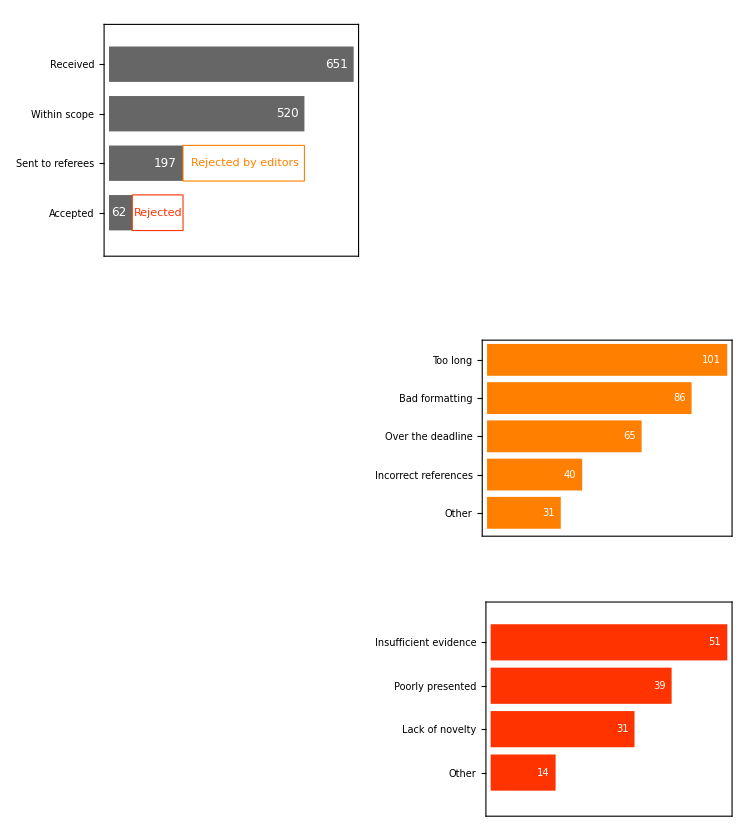

```mathematica
numReceived={651,520,197,62};
percReceived=N[numReceived/Total[numReceived]];
receivedActions={"Received","Within scope","Sent to referees","Accepted"};

numNotSent={101,86,65,40,31};
notSentCategories={"Too long","Bad formatting","Over the deadline","Incorrect references","Other"};

rejectedCategories={"Insufficient evidence","Poorly presented","Lack of novelty","Other"};
numRejected={51,39,31,14};

(**************************************************************)
(* Code for main plot *)

rejEdColour=RGBColor[1,0.5,0,1];
rejColour=RGBColor[1,0.2,0,1];

grayColour=RGBColor[0.4,0.4,0.4,1];
receivedPlot=BarChart[Reverse[numReceived],
ChartLabels->Map[Style[#,grayColour,12]&, Reverse[receivedActions]],
	BarOrigin->Left,
	BarSpacing->0.4,
	Frame->{True,True,False,False},
	FrameStyle->RGBColor[1,1,1,0],
	FrameTicks->{None, Automatic},
	ChartStyle->Directive[EdgeForm[None], grayColour],
	LabelingFunction->(Placed[Style[#,FontSize->12, White],Right]&),
	PlotLabel->Style["\n", 18],
AspectRatio->1.1,

	Epilog->{
		Style[Text["Number of papers processed",
		           {-235,5}, {-1,-1}],
		      FontSize->16, GrayLevel[0.2]],
		Style[Text["January - December 2020",
		           {-235,4.75}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]],

	White,
	EdgeForm[Directive[Dashed,rejEdColour,Thick]],
	Rectangle[{197,1.64}, {520,2.36}],
	rejEdColour,
	Style[Text["Rejected by editors",{363,2}],FontSize->11],

	White,
	EdgeForm[Directive[Dashed,rejColour,Thick]],
	Rectangle[{62,0.64}, {197,1.36}],
	rejColour,
	Style[Text["Rejected",{130,1}],FontSize->11]
	}
];

(* Export[FileNameJoin[{NotebookDirectory[],"receivedPlot.png"}],Magnify[receivedPlot,4]]; *)

(**************************************************************)
(* Code for "rejected by editors" plot *)

rejEdFS=10;
rejEdPlot=BarChart[Reverse[numNotSent],
ChartLabels->Map[Style[#,grayColour,rejEdFS]&, Reverse[notSentCategories]],
	BarOrigin->Left,
	BarSpacing->0.2,
	Frame->{True,True,False,False},
	FrameStyle->RGBColor[1,1,1,0],
	FrameTicks->{None, Automatic},
	ChartStyle->Directive[EdgeForm[None],rejEdColour ],
	LabelingFunction->(Placed[Style[#,FontSize->rejEdFS, White],Right]&),
	PlotLabel->Style["\n", 16],
AspectRatio->1.0/2,
	
	Epilog->{
		Style[Text["Why editors reject papers",
		           {-38,6.5}, {-1,-1}],
		      FontSize->16, GrayLevel[0.2]],
		Style[Text["Number of papers rejected by editors",
		           {-38,5.9}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]]
}
];
(* Export[FileNameJoin[{NotebookDirectory[],"rejEdPlot.png"}],Magnify[rejEdPlot,4]]; *)

(**************************************************************)
(* Code for "rejected by referees" plot *)

rejPlot=BarChart[Reverse[numRejected],
ChartLabels->Map[Style[#,grayColour,rejEdFS]&, Reverse[rejectedCategories]],
	BarOrigin->Left,
	BarSpacing->0.2,
	Frame->{True,True,False,False},
	FrameStyle->RGBColor[1,1,1,0],
	FrameTicks->{None, Automatic},
	ChartStyle->Directive[EdgeForm[None],rejColour ],
	LabelingFunction->(Placed[Style[#,FontSize->rejEdFS, White],Right]&),
	PlotLabel->Style["\n", 16],
AspectRatio->1.0/2,
	
	Epilog->{
		Style[Text["Why referees reject papers",
		           {-19.8,5.5}, {-1,-1}],
		      FontSize->16, GrayLevel[0.2]],
		Style[Text["Number of papers rejected by referees",
		           {-19.8,4.9}, {-1,-1}],
		      FontSize->12, GrayLevel[0.5]]
}
];
(* Export[FileNameJoin[{NotebookDirectory[],"rejPlot.png"}],Magnify[rejPlot,4]]; *)

(***************************************************************)
(* Code to create the final plot *)


Graphics[{
Inset[receivedPlot,{0,1.05},{Left,Top},1],
Inset[rejEdPlot,{1.05,0.5},{Left,Bottom},1],
Inset[rejPlot,{1.05,0},{Left,Bottom},1]
},

ImageSize->Full,

PlotLabel->"\n\n",
Epilog->{
Style[Text["Most papers are rejected because of",{0,1.12},{-1,-1}],
  FontSize->24],
Style[Text["length and lack of evidence presented",{0,1.05},{-1,-1}],
  FontSize->24, Bold]
}
]

(*

receivedPlotIm=Import[FileNameJoin[{NotebookDirectory[],"receivedPlot.png"}]];
rejPlotIm=Import[FileNameJoin[{NotebookDirectory[],"rejPlot.png"}]];
rejEdPlotIm=Import[FileNameJoin[{NotebookDirectory[],"rejEdPlot.png"}]];

Graphics[{
Inset[receivedPlotIm,{0,1.05},{Left,Top},1],
Inset[rejEdPlotIm,{1.05,0.5},{Left,Bottom},1],
Inset[rejPlotIm,{1.05,0},{Left,Bottom},1]
},

PlotLabel->"\n\n",
Epilog->{
Style[Text["Most papers are rejected because of",{0,1.16},{-1,-1}],
  FontSize->16],
Style[Text["length and lack of evidence presented",{0,1.05},{-1,-1}],
  FontSize->16, Bold]
}
]
*)
```